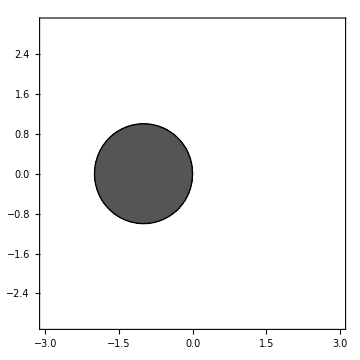
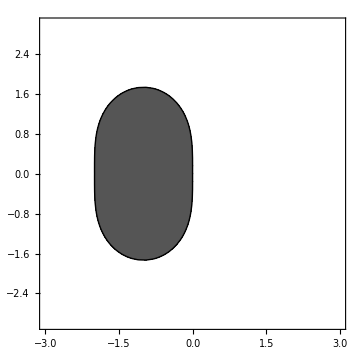
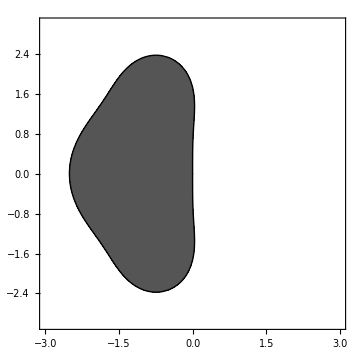
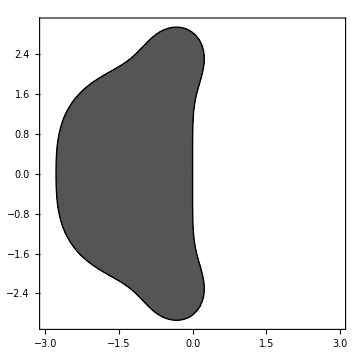

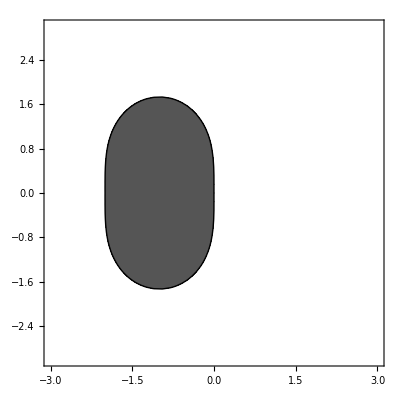

```mathematica
r[z_,s_]:=(Normal@Series[Exp[ξ],{ξ,0,s}])/.ξ->z
Table[RegionPlot[Abs@r[x+I y,s]<1,{x,-3,3},{y,-3,3},BoundaryStyle->Black,PlotStyle->Lighter@Black,ImageSize->Medium],{s,1,4}]
```

```mathematica
r[x+I y]
```

1+x+1/2 (x+ⅈ y)^2+ⅈ y